We want to check if various "averages" of μ1 and μ2 are maximized by the equilateral triangle. We have
(μ1+μ2)/2≥√(μ1 μ2)≥2/(1/μ1+1/μ2)
Arithmetic average should not be maximized, since it is not maximized by the square among rectangles or by the circle among all domains. Harmonic average is maximized by the square and the circle, so it should be also maximized by the equilateral triangle. It is not clear for geometric average, but it is maximized by the square.

## Proof for the harmonic average

We need 2 test functions, that are integrable to 0, and have orthogonal gradients. This follows from Bandle's book, page 99 (general) and 101 (Neumann case). We get
2/(1/μ1+1/μ2) ≤2/(1/R[v1]+1/R[v2]), where R[*] is the Rayleigh quotient and v1, v2 are as above. 
We consider a triangle with vertices (0,0), (1,0) and (a,b). For uniqueness we can later assume that a≤1/2 and a^2+b^2≥1.

### Linear test functions

#### Initial definitions

```mathematica
int[v_]:=Integrate[v,{y,0,b},{x,a y/b,(a-1)y/b+1}];
R[v_]:=int[D[v,x]^2+D[v,y]^2]/int[v^2];
A=b/2;
```

#### Proof

Linear test functions provide amasingly good upper bounds not only for the first eigenvalue, but also for the harmonic average. We could also use one linear and one quadratic function. This would be better for wide triangles, but we would need at least 2 sets of test functions (one in x and one in y).

```mathematica
v1=x+c;
v2=y+d;
v1=v1/.Solve[int[v1]==0,{c}][[1]]
v2=v2/.Solve[int[v2]==0,{d}][[1]]
int[D[v1,x]D[v2,x]+D[v1,y]D[v2,y]]
bound1=2/(1/R[v1]+1/R[v2])//Simplify
cond=(A bound1≤(4 π^2)/(3 √3))
```

1/3 (-1-a)+x

-b/3+y

0

36/(1-a+a^2+b^2)

(18 b)/(1-a+a^2+b^2)≤(4 π^2)/(3 √3)

Hence we can handle any triangle satisfying the above condition (outside of a circle).

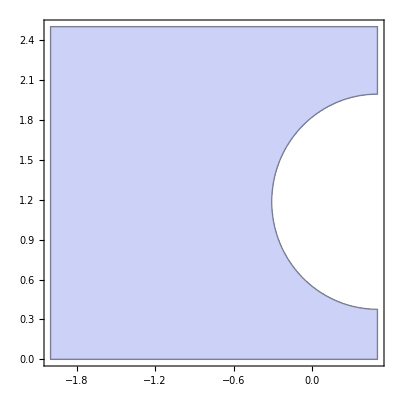

```mathematica
RegionPlot[cond,{a,-2,1/2},{b,0,5/2}]
```

We can use transplantation on the above rectangle.

### Exact eigenfunctions

#### Initial definitions

Linear transformations

```mathematica
LT[{p1_,p2_,p3_},{q1_,q2_,q3_}]:=Module[{ff},
ff[x_]={x.{aa,bb}+cc ,x.{dd,ee}+ff};
AffineTransform[{{{aa,bb},{dd,ee}},{cc,ff}}]/.Solve[{ff[p1]==q1,ff[p2]==q2,ff[p3]==q3},{aa,bb,cc,dd,ee,ff}][[1]]
];
TR[p_]:={{0,0},{1,0},p};
LT1[p_,q_]:=LT[TR[p],TR[q]];
Change[p_,q_]:=Thread[{x,y}->LT[p,q][{x,y}]];
TEquilateral=TR[{1/2,√3/2}];
TAB=TR[{a,b}];
```

Trigonometric integrals

```mathematica
intS=Integrate[Sin[AA+BB x],{x,a,b}];
intS2=Integrate[y Sin[AA+BB y],{y,a,b}];
s1[a_,b_] = (X_. Sin[AA_.+BB_ x]->X intS);
s2[a_,b_]= (X_. Cos[AA_.+BB_ x]->(s1[a,b][[2]]/.Cos[Y_]->-Sin[Y]));
s3[a_,b_] = (X_. Sin[AA_.+BB_ y]->X (intS/.x->y));
s4[a_,b_] = (X_. y Sin[AA_.+BB_ y]->X intS2);
s5[a_,b_] = (X_. Cos[AA_.+BB_ y]->(s3[a,b][[2]]/.Cos[Y_]->-Sin[Y]));
s6[a_,b_] = (X_. y Cos[AA_.+BB_ y]->(s4[a,b][[2]]/.{Cos[Y_]->-Sin[Y],Sin[Y_]->Cos[Y]}));

TrigIntegrate[fff_,{inty_,intx_}]:=(
ff=TrigReduce[fff];
ff=Expand[ff];
ff=ff/.Sin[A_]:>Sin[Collect[A,{x},Simplify]]/.Cos[A_]:>Cos[Collect[A,{x},Simplify]];
ff=Replace[ff,{s1@@intx,s2@@intx,X_->(intx[[2]]-intx[[1]])X},1];
ff=ff/.Sin[A_]:>Sin[Collect[A,{y},Simplify]]/.Cos[A_]:>Cos[Collect[A,{y},Simplify]];
ff=Expand[ff];
ff=Replace[ff,{s4@@inty,s6@@inty,s3@@inty,s5@@inty,A_. y->A (inty[[2]]^2-inty[[1]]^2)/2,X_->(inty[[2]]-inty[[1]]) X},1];
ff/.Sin[A_]:>Sin[Collect[A,{y},Simplify]]/.Cos[A_]:>Cos[Collect[A,{y},Simplify]]);

trigint[v_]:=TrigIntegrate[v,{{0,b},{a y/b,(a-1)y/b+1}}];
trigR[v_]:=trigint[D[v,x]^2+D[v,y]^2]/trigint[v^2];
```

#### Proof

Unfortunately linear transplantation does not preserve orthogonality of the gradient. Hence to fix this we need to use 2 eigenfunctions of the equilateral triangle plus one correcting function. This could be anything, but the eigenfunction of the right isosceles triangle should help with nonisosceles triangles.

```mathematica
z=π/3(2x-1);
t=π(1-2/√3 y);
h[S01]=2Cos[z]Cos[t]+Cos[2z];
h[A01]=2Sin[z]Cos[t]-Sin[2z];
```

Transplantation

```mathematica
f1=h[A01]/.Change[TAB,TEquilateral];
f2=h[S01]/.Change[TAB,TEquilateral];
```

Test functions

```mathematica
c1=trigint[D[f1,x]D[f2,x]+D[f1,y]D[f2,y]]//Simplify
c2=trigint[D[f2,x]^2+D[f2,y]^2]//Simplify
trigint[D[c2 f1-c1 f2,x]D[f2,x]+D[c2 f1-c1 f2,y]D[f2,y]]//Simplify
t1=b(c2 f1 -c1 f2)//Simplify;
t2=f2;
trigint[t1]
trigint[t2]
trigint[D[t1,x]D[t2,x]+D[t1,y]D[t2,y]]//Simplify
```

(81 √3 (-1+2 a))/(32 b)

(243+64 π^2+a (486-64 π^2)+a^2 (-486+64 π^2)+b^2 (-486+64 π^2))/(96 b)

0

0

0

«1 more identical outputs»

Bound

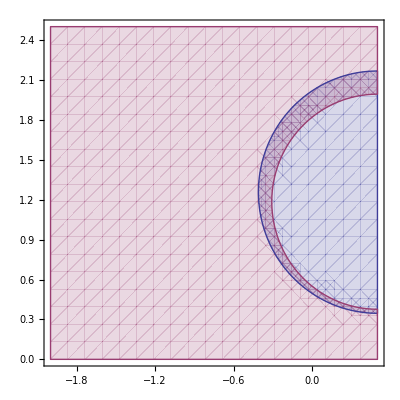

```mathematica
bound2=2/(1/trigR[t1]+1/trigR[t2])//Cancel//Simplify;
RegionPlot[{A bound2<(4 π^2)/(3 √3),cond},{a,-2,1/2},{b,0,5/2}]
```

Proof

```mathematica
(A bound2-(4 π^2)/(3 √3)//Together//Simplify//Denominator)>0//Reduce
A bound2-(4 π^2)/(3 √3)//Together//Simplify//Numerator
%/.a->1/2-a/.b->√3/2+b//Factor
bd=%/(a^2+b^2)//Collect[#,{a,b},Simplify]&
```

a∈Reals&&b>0

-59049+1024 π^4-1024 √3 b π^4-1024 √3 b^3 π^4+a^3 (118098-2048 π^4)+a^4 (-59049+1024 π^4)+b^4 (-59049+1024 π^4)+b^2 (59049+2048 π^4)+2 a (59049-1024 π^4+512 √3 b π^4+b^2 (59049-1024 π^4))+a^2 (-177147+3072 π^4-1024 √3 b π^4+2 b^2 (-59049+1024 π^4))

(a^2+b^2) (-177147-59049 a^2-118098 √3 b-59049 b^2+1536 π^4+1024 a^2 π^4+1024 √3 b π^4+1024 b^2 π^4)

3 (-59049+512 π^4)+2 √3 b (-59049+512 π^4)+a^2 (-59049+1024 π^4)+b^2 (-59049+1024 π^4)

This (bd) should be negative if

```mathematica
cnd=!cond/.a->1/2-a/.b->√3/2+b//Simplify
```

(18 (√3+2 b))/(3+2 a^2+2 √3 b+2 b^2)>(4 π^2)/(3 √3)

We can solve for a^2  and plug above

```mathematica
Subtract@@cnd
(Subtract@@cnd//Together//Denominator)>0//Reduce
Subtract@@cnd//Together//Numerator
sqr=Reduce[%>0/.a^2->c,a,Reals]/.c->a^2
```

(18 (√3+2 b))/(3+2 a^2+2 √3 b+2 b^2)-(4 π^2)/(3 √3)

(a|b)∈Reals

-2 (-81 √3-162 b+6 √3 π^2+4 √3 a^2 π^2+12 b π^2+4 √3 b^2 π^2)

a^2<(81 √3+162 b-6 √3 π^2-12 b π^2-4 √3 b^2 π^2)/(4 √3 π^2)

```mathematica
bd//Collect[#,{a,b},Sign]&
```

-1+a^2-b+b^2

Hence the value of bd will increase if we use the above inequality

```mathematica
Rule@@sqr
bd/.%//Simplify
Simplify[%<0,{b>-√3/2}]
```

a^2→(81 √3+162 b-6 √3 π^2-12 b π^2-4 √3 b^2 π^2)/(4 √3 π^2)

(27 (3+2 √3 b) (-59049-4374 π^2+1024 π^4))/(4 π^2)

True

It is negative. qed

## Arithmetic and geometric averages

### Arithmetic

I am not sure if it is not true that arithmetic average is maximized by the equilateral triangle. Right isosceles triangle has smaller average, and right triangle with angle π/3 has exactly the same average as equilateral. I could not find a counterexample.
To find an upper bound for arithmetic average we need 2 test functions that integrate to 0 and which are orthogonal (page 98 in Bandle's book). The bound is equal to the sum of te Reyleigh quotients.

### Geometric

We can use the above to find a bound for the geometric average (Geometric^2 = Arithmetic*Harmonic). We can take 2 orthogonal test functions for arithmetic average and 2 "gradient orthogonal" functions for harmonic average and get a bound for geometric average (4 test functions).
   Alternatively we could try to find 2 test functions that are orthogonal and "gradient orthogonal" and then the bound is R[v1] R[v2]. Unfortunately, the mixture of exact eigenfunctions has this property only for isosceles triangles, but even in this case the bound is weaker then μ1μ2 for equilateral. The same happens for the linear test functions.

1/288 √((-531441+9216 π^4+16 b^4 (-59049+1024 π^4)+24 b^2 (59049+1024 π^4))/b^2)

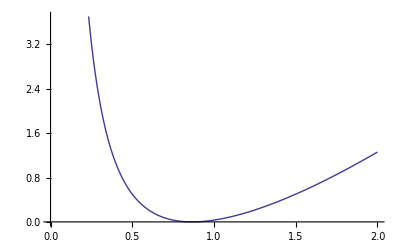

6 √3

2.79468

```mathematica
√(A^2 trigR[t1]trigR[t2])/.a->1/2//Simplify
Plot[%-4π^2/(3 √3),{b,0,2}]
√(A^2R[v1]R[v2])/.a->1/2//Simplify
%-4π^2/(3 √3)//N
```

It is probably possible to find better test functions, but for now, I have no idea if arithmetic and/or geometric averages are maximized by the equilateral triangle.

## Problem with integration

All trigonometric integrals are extremely slow in Mathematica 5.1 and newer. This is why I am using special function (initial definitions in exact eigenvalues section) to integrate the exact eigenfunctions.

```mathematica
Timing[trigint[t2]][[1]]
Timing[int[t2]][[1]]
Timing[trigint[t2]][[1]]
Timing[int[t2]][[1]]
```

0.047

4.36

0.015

0.422

```mathematica
Timing[trigR[t2]][[1]]
Timing[R[t2]][[1]]
```

0.844

$Aborted